```mathematica
Integrate[ Exp[I*(-ω*t-π/2)] * I^(a+b)*BesselJ[a, A]*BesselJ[b,A]*Exp[I*(a*(π-ω*t)+b*(2*π-2*ω*t))] + Exp[-I*(-ω*t-π/2)] * (-I)^(a+b)*BesselJ[a, A]*BesselJ[b,A]*Exp[-I*(a*(π-ω*t)+b*(2*π-2*ω*t))], {t,]
```

(ⅇ^(-ⅈ ((a+2 b) π+(1+a+2 b) t ω)) (ⅇ^(1/2 ⅈ (5 a+9 b) π)+(-ⅈ)^(a+b) ⅇ^(2 ⅈ (1+a+2 b) t ω)) BesselJ[a,A] BesselJ[b,A])/((1+a+2 b) ω)

((-ⅈ)^b+ⅈ^b) t BesselJ[-1-2 b,A] BesselJ[b,A]

0.05

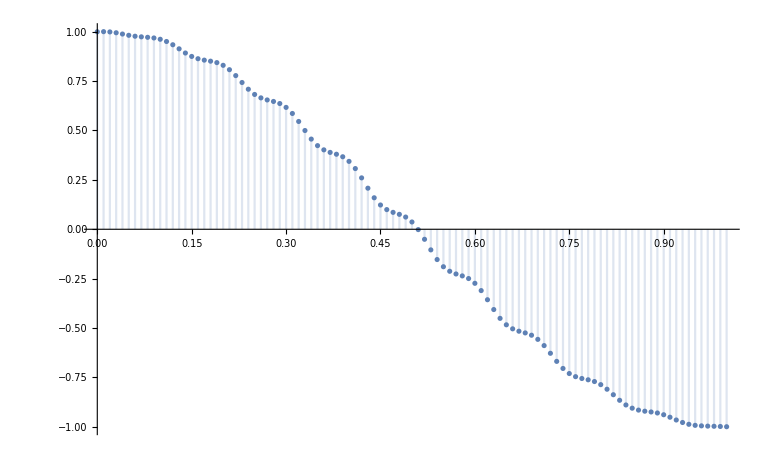

```mathematica
Integrate[ Exp[I*(-ω*t-π/2)] * I^(-1-2b+b)*BesselJ[-1-2b, A]*BesselJ[b,A]*Exp[I*((-1-2b)*(π-ω*t)+b*(2*π-2*ω*t))] + Exp[-I*(-ω*t-π/2)] * (-I)^(-1-2b+b)*BesselJ[-1-2b, A]*BesselJ[b,A]*Exp[-I*((-1-2b)*(π-ω*t)+b*(2*π-2*ω*t))], t]
```

```mathematica
res =Integrate[ Exp[I*(-ω*t-π/2)] * I^(a+b)*BesselJ[a, A]*BesselJ[b,A]*Exp[I*(a*(π-ω*t)+b*(2*π-2*ω*t))] + Exp[-I*(-ω*t-π/2)] * (-I)^(a+b)*BesselJ[a, A]*BesselJ[b,A]*Exp[-I*(a*(π-ω*t)+b*(2*π-2*ω*t))], t];
```